```mathematica
r=2;
v1=4;
v2=2;
L1[ϕ_]:=ϕ*r;(*Bord*)
L2[ϕ_]:=Abs[r] √(2+2Cos[2*ϕ]);(*ligne droit*)
tempsTot[ϕ_]:=(2*L1[ϕ])/v1+L2[ϕ]/v2
```

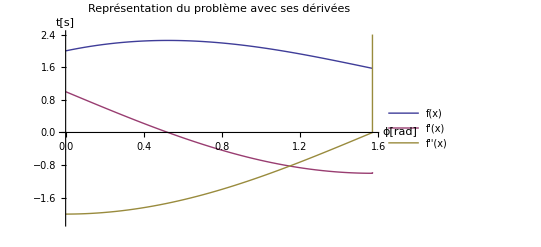

```mathematica
Plot[{tempsTot[ϕ],tempsTot'[ϕ],tempsTot''[ϕ]},{ϕ,0,π/2},PlotRange->{{0,π/2},{-r-r/10,r+r/5}},PlotLegends->{"f(x)","f'(x)","f''(x)"},AxesStyle->Arrowheads[0.02],AxesLabel->{"ϕ[rad]","t[s]"},PlotLabel->"Représentation du problème avec ses dérivées"]
```